1+1 Teukolsky equation in hyperboloidal slices of Kerr spacetime

## Initial Set Up

We start with the 1+1 Teukolsky equation in hyperboloidal slices of Kerr spacetime

```mathematica
Barack39MinimalGauge=(l+l^2-s (1+s)-2 σ^2 χ^2+σ (1+s+2 ⅈ m χ)) Subscript[ψ, l][τ,σ]+σ (-2+s (-2+σ)+σ (3+2 ⅈ m χ-4 σ χ^2)) Derivative[0,1][Subscript[ψ, l]][τ,σ]+σ^2 (-1+σ-σ^2 χ^2) Derivative[0,2][Subscript[ψ, l]][τ,σ]+ⅈ s χ Subscript[c, "-"][l,s] Derivative[1,0][Subscript[ψ, -1+l]][τ,σ]+(s (-1+σ)+2 σ+ⅈ χ (m+2 m σ+ⅈ σ (1+3 σ) χ)+ⅈ s χ Subscript[c, 0][l,s]) Derivative[1,0][Subscript[ψ, l]][τ,σ]+ⅈ s χ Subscript[c, "+"][l,s] Derivative[1,0][Subscript[ψ, 1+l]][τ,σ]+(-1-σ^2 (-2+(1+2 σ) χ^2)) Derivative[1,1][Subscript[ψ, l]][τ,σ]-χ^2 Subscript["C", "--"][l,s] Derivative[2,0][Subscript[ψ, -2+l]][τ,σ]-χ^2 Subscript["C", "-"][l,s] Derivative[2,0][Subscript[ψ, -1+l]][τ,σ]+(-((1+σ) (-1+σ χ^2))-χ^2 Subscript["C", 0][l,s]) Derivative[2,0][Subscript[ψ, l]][τ,σ]-χ^2 Subscript["C", "+"][l,s] Derivative[2,0][Subscript[ψ, 1+l]][τ,σ]-χ^2 Subscript["C", "++"][l,s] Derivative[2,0][Subscript[ψ, 2+l]][τ,σ];
Subscript[δ, l_,k_]=KroneckerDelta[l,k];
```

We define the following components which we will use to write the Teukolsky equation in matrix form

```mathematica
(*band={Subscript[δ, l-2,k],Subscript[δ, l-1,k],Subscript[δ, l,k],Subscript[δ, l+1,k],Subscript[δ, l+2,k]};
Subscript[Α, l_,k_][σ_]=Coefficient[Barack39MinimalGauge,{Subscript[ψ, -2+l]^(2,0)[τ,σ],Subscript[ψ, -1+l]^(2,0)[τ,σ],Subscript[ψ, l]^(2,0)[τ,σ],Subscript[ψ, 1+l]^(2,0)[τ,σ],Subscript[ψ, 2+l]^(2,0)[τ,σ]}].band;
Subscript[Β, l_,k_][σ_]=(Coefficient[-Barack39MinimalGauge,{Subscript[ψ, -2+l]^(1,0)[τ,σ],Subscript[ψ, -1+l]^(1,0)[τ,σ],Subscript[ψ, l]^(1,0)[τ,σ],Subscript[ψ, 1+l]^(1,0)[τ,σ],Subscript[ψ, 2+l]^(1,0)[τ,σ]}]//FullSimplify).band;
Subscript[Γ, l_,k_][σ_]=(Coefficient[-Barack39MinimalGauge,{Subscript[ψ, -2+l]^(1,1)[τ,σ],Subscript[ψ, -1+l]^(1,1)[τ,σ],Subscript[ψ, l]^(1,1)[τ,σ],Subscript[ψ, 1+l]^(1,1)[τ,σ],Subscript[ψ, 2+l]^(1,1)[τ,σ]}]//FullSimplify).band;
Subscript[Δ, l_,k_][σ_]=(Coefficient[-Barack39MinimalGauge,{Subscript[ψ, -2+l]^(0,1)[τ,σ],Subscript[ψ, -1+l]^(0,1)[τ,σ],Subscript[ψ, l]^(0,1)[τ,σ],Subscript[ψ, 1+l]^(0,1)[τ,σ],Subscript[ψ, 2+l]^(0,1)[τ,σ]}]//FullSimplify).band;
Subscript[Ε, l_,k_][σ_]=(Coefficient[-Barack39MinimalGauge,{Subscript[ψ, -2+l]^(0,2)[τ,σ],Subscript[ψ, -1+l]^(0,2)[τ,σ],Subscript[ψ, l]^(0,2)[τ,σ],Subscript[ψ, 1+l]^(0,2)[τ,σ],Subscript[ψ, 2+l]^(0,2)[τ,σ]}]//FullSimplify).band;
Subscript[Ζ, l_,k_][σ_]=(Coefficient[-Barack39MinimalGauge,{Subscript[ψ, -2+l][τ,σ],Subscript[ψ, -1+l][τ,σ],Subscript[ψ, l][τ,σ],Subscript[ψ, 1+l][τ,σ],Subscript[ψ, 2+l][τ,σ]}]//FullSimplify).band;*)
```

```mathematica
Αdiag[σ_]=Coefficient[Barack39MinimalGauge,Derivative[2,0][Subscript[ψ, l]][τ,σ]]/.{Subscript["C", 0][l,s]->0}//FullSimplify
Αdiagl[l_]=Coefficient[Coefficient[Barack39MinimalGauge,Derivative[2,0][Subscript[ψ, l]][τ,σ]],Subscript["C", 0][l,s]]Subscript["C", 0][l,s]//FullSimplify
Αsupdiag[l_]=Coefficient[Barack39MinimalGauge,Derivative[2,0][Subscript[ψ, l+1]][τ,σ]]//FullSimplify
Αsupsupdiag[l_]=Coefficient[Barack39MinimalGauge,Derivative[2,0][Subscript[ψ, l+2]][τ,σ]]//FullSimplify
Αsubdiag[l_]=Coefficient[Barack39MinimalGauge,Derivative[2,0][Subscript[ψ, l-1]][τ,σ]]//FullSimplify
Αsubsubdiag[l_]=Coefficient[Barack39MinimalGauge,Derivative[2,0][Subscript[ψ, l-2]][τ,σ]]//FullSimplify

Βdiag[σ_]=Coefficient[-Barack39MinimalGauge,Derivative[1,0][Subscript[ψ, l]][τ,σ]]/.{Subscript[c, 0][l,s]->0}//FullSimplify
Βdiagl[l_]=Coefficient[Coefficient[-Barack39MinimalGauge,Derivative[1,0][Subscript[ψ, l]][τ,σ]],Subscript[c, 0][l,s]]Subscript[c, 0][l,s]//FullSimplify
Βsupdiag[l_]=Coefficient[-Barack39MinimalGauge,Derivative[1,0][Subscript[ψ, l+1]][τ,σ]]//FullSimplify
Βsubdiag[l_]=Coefficient[-Barack39MinimalGauge,Derivative[1,0][Subscript[ψ, l-1]][τ,σ]]//FullSimplify

Γdiag[σ_]=Coefficient[-Barack39MinimalGauge,Derivative[1,1][Subscript[ψ, l]][τ,σ]]//FullSimplify;

Δdiag[σ_]=Coefficient[-Barack39MinimalGauge,Derivative[0,1][Subscript[ψ, l]][τ,σ]]//FullSimplify;

Εdiag[σ_]=Coefficient[-Barack39MinimalGauge,Derivative[0,2][Subscript[ψ, l]][τ,σ]]//FullSimplify;

Ζdiag[σ_]=Coefficient[-Barack39MinimalGauge,Subscript[ψ, l][τ,σ]]/.{l->0}//FullSimplify;
Ζdiagl[l_]=Coefficient[-Barack39MinimalGauge,Subscript[ψ, l][τ,σ]]/.{s->0,σ->0}//FullSimplify;
```

1+σ-σ (1+σ) χ^2

-χ^2 C_0[l,s]

-χ^2 C_+[l,s]

-χ^2 C_(++)[l,s]

-χ^2 C_-[l,s]

-χ^2 C_(--)[l,s]

s-2 σ-s σ-ⅈ m (1+2 σ) χ+σ (1+3 σ) χ^2

-ⅈ s χ c_0[l,s]

-ⅈ s χ c_+[l,s]

-ⅈ s χ c_-[l,s]

```mathematica
(* Eqs. (34), (35), (37) of https://arxiv.org/pdf/gr-qc/9908005.pdf;
We multiplied Barack's definitions of the coupling coefficients C by a factor of 4;*)
cm2[l_,s_]=If[l==0,0,(Ramp[l^2-s^2]Ramp[l^2-m^2])/(l^2(2l-1)(2l+1))];
Subscript[c, "-"][l_,s_]=√cm2[l,s];
Subscript[c, 0][l_,s_]=If[l m s==0,0,-(m s)/(l (l+1))];
Subscript[c, "+"][l_,s_]=Subscript[c, "-"][l+1,s];
cp2[l_,s_]=cm2[l+1,s];
Subscript["C", "++"][l_,s_]=4 Subscript[c, "+"][l,s]Subscript[c, "+"][l+1,s];
Subscript["C", "+"][l_,s_]=4 Subscript[c, "+"][l,s](Subscript[c, 0][l,s]+Subscript[c, 0][l+1,s]);
Subscript["C", 0][l_,s_]=If[(l<Abs[s])||(l<Abs[m]),0,4(cm2[l,s]+cp2[l,s]+(Subscript[c, 0][l,s])^2-1)];
Subscript["C", "-"][l_,s_]=If[l==0,0,4 Subscript[c, "-"][l,s](Subscript[c, 0][l,s]+Subscript[c, 0][l-1,s])];
Subscript["C", "--"][l_,s_]=If[(Abs[m]≤l≤Abs[m]+1)||((Abs[s]≤l≤Abs[s]+1)),0,4 Subscript[c, "-"][l,s]Subscript[c, "-"][l-1,s]];
```

## Setting parameter values

```mathematica
s=2;
m=0;
χ =1/4;
n=120; (*number of gridpoints*)
l0 = Max[Abs[s],Abs[m]];
numberLmodes =4;
lmax=numberLmodes + l0 -1;
GridType = 1; (*number of finite difference grid, 1 for pseudo spectral*)
```

```mathematica
l0
```

2

```mathematica
Min[Abs[s],Abs[m]]
```

0

## Creating Matrix L

```mathematica
a=0;
b=2/(1+√(1-4 χ^2));
If[GridType==0,
{σσ = Subdivide[a,b,n];
D1=NDSolve`FiniteDifferenceDerivative[Derivative[1],σσ,"DifferenceOrder"->8,PeriodicInterpolation->False]@"DifferentiationMatrix";
D2=NDSolve`FiniteDifferenceDerivative[Derivative[2],σσ,"DifferenceOrder"->8,PeriodicInterpolation->False]@"DifferentiationMatrix";
},
{
Z=Table[Sin[(π (2i-n))/(2n)],{i,0,n}];
σσ = ((b+a)+(b-a)Z)/2//N;
Subscript[cc, i_]=1+KroneckerDelta[i,0]+KroneckerDelta[i,n];
D1=(2/(b-a))*Table[If[i≠j,(Subscript[cc, i](-1)^(i+j))/(2 Subscript[cc, j] Sin[(i+j)π/(2n)]Sin[(i-j)π/(2n)]),Which[i==0,-((2 n^2+1)/6),i==n,(2 n^2+1)/6,True,(-Z[[j+1]])/(2 Sin[j π/n]^2)]],{i,0,n},{j,0,n}];
D2=((2/(b-a))^2)*Table[If[i≠j,Which[(i==0),2/3(-1)^j/Subscript[cc, j]((2 n^2+1)(1+Z[[j+1]])-6)/(1+Z[[j+1]])^2,i==n,2/3(-1)^(j+n)/Subscript[cc, j]((2 n^2+1)(1-Z[[j+1]])-6)/(1-Z[[j+1]])^2,True,(-1)^(i+j)/Subscript[cc, j](Z[[i+1]]^2+Z[[i+1]]Z[[j+1]]-2)/((1-Z[[i+1]]^2)(Z[[i+1]]-Z[[j+1]])^2)],If[(i==0)||(i==n),(n^4-1)/15,-((n^2-1)(1-Z[[i+1]]^2)+3)/(3(1-Z[[i+1]]^2)^2)]],{i,0,n},{j,0,n}];
}
];
D1 = Developer`ToPackedArray[D1, Complex]; 
D2 = Developer`ToPackedArray[D2, Complex]; 
ll=Table[l,{l,l0,numberLmodes + l0 -1}];
Ilk=IdentityMatrix[numberLmodes];
Iij=IdentityMatrix[n+1];
Alk=Table[Subscript[δ, l-2,k] Αsubsubdiag[l]+Subscript[δ, l-1,k] Αsubdiag[l]+Subscript[δ, l,k] Αdiagl[l]+Subscript[δ, l+1,k] Αsupdiag[l]+Subscript[δ, l+2,k] Αsupsupdiag[l],{l,l0,lmax}, {k,l0, lmax}];
Blk=Table[Subscript[δ, l-1,k] Βsubdiag[l]+Subscript[δ, l,k] Βdiagl[l]+Subscript[δ, l+1,k] Βsupdiag[l],{l,l0,lmax}, {k,l0, lmax}];
```

```mathematica
AbsoluteTiming[
A=SparseArray[N[KroneckerProduct[Alk,Iij]+KroneckerProduct[Ilk,Αdiag[σσ]*Iij]]];
Ν=SparseArray[N[KroneckerProduct[Blk,Iij]+KroneckerProduct[Ilk,Βdiag[σσ]*Iij+Γdiag[σσ]*D1]]];
Μ=SparseArray[N[KroneckerProduct[Ζdiagl[ll]*Ilk,Iij]+KroneckerProduct[Ilk,Δdiag[σσ]*D1+Εdiag[σσ]*D2+Ζdiag[σσ]*Iij]]];
Ainverse=SparseArray[Inverse[A]];
]
```

{0.198415,Null}

```mathematica
lenuse = Length[A];(*n*numberLmodes*)
ONN=SparseArray[N[ConstantArray[0,{lenuse,lenuse}]]];
INN=SparseArray[N[IdentityMatrix[lenuse]]];

L2N2N=Developer`ToPackedArray[ArrayFlatten[{{ONN,INN},{Ainverse.Μ,Ainverse.Ν}}]];
```

## Evolution Test

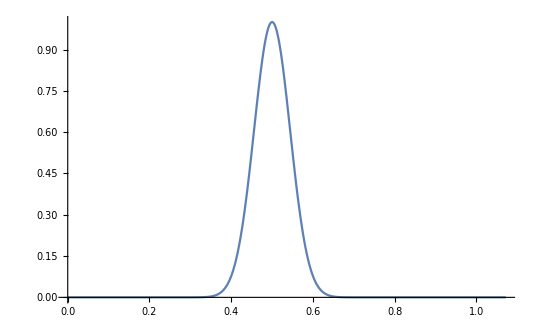

```mathematica
c=256;
w=0.5;
f[x_]=Exp[-c(x-w)^2];
SetAttributes[f,Listable]
Plot[f[x],{x,a,b},PlotRange->All]
```

```mathematica
D1Error = Max[Abs[D1.f[σσ]-f'[σσ]]]
D2Error = Max[Abs[D2.f[σσ]-f''[σσ]]]
```

5.50671×10^-14

8.73115×10^-11

```mathematica
m1=10000;
tend = 2;
Δt=tend/m1;
T=Subdivide[0,tend,m1]//N;
```

```mathematica
Δx = σσ[[2]]-σσ[[1]]//N;
```

```mathematica
Δt/Δx
```

1.08909

```mathematica
position = ConstantArray[f[σσ]*0,{numberLmodes}];
position[[1]] = f[σσ];
position = Transpose[position] ;
Dimensions[position]
```

{121,4}

```mathematica
position = ConstantArray[f[σσ],{numberLmodes}];
position = Transpose[position] ;
Dimensions[position]
```

{101,4}

```mathematica
velocity = ConstantArray[0,{numberLmodes, n+1}];
velocity = Transpose[velocity] ;
Dimensions[velocity]
```

{121,4}

```mathematica
statevector =Flatten[Join[Transpose[position],Transpose[velocity]]];
statematrix  =Developer`ToPackedArray[ ConstantArray[statevector,{m1}],Complex];
```

```mathematica
bherminvert = Developer`ToPackedArray[IdentityMatrix[Length[L2N2N]] -Δt/2*L2N2N.(IdentityMatrix[Length[L2N2N]]-Δt/6*L2N2N),Complex];
BHerm = Developer`ToPackedArray[Inverse[bherminvert].(Δt*L2N2N ), Complex];
```

```mathematica
AbsoluteTiming[Do[statematrix[[i+1]]=statematrix[[i]]+ BHerm.statematrix[[i]],
{i,1,m1-1}]]
```

{0.937156,Null}

```mathematica
PositionResults = Table[statematrix[[All,1 + (n+1)*(i - 1);;(n+1) + (n+1)*(i - 1)]],{i,numberLmodes}];
MomentumResults = Table[statematrix[[All,1 + (n+1)*(i - 1)+(n+1)*numberLmodes;;(n+1) + (n+1)*(i - 1)+(n+1)*numberLmodes]],{i,numberLmodes}];
FinalResults = {PositionResults,MomentumResults};
```

```mathematica
Export["C:\\Users\\brays\\PHD_CodeWork\\Data\\S=2.m.gz",FinalResults]//AbsoluteTiming
```

{291.564,C:\Users\brays\PHD_CodeWork\Data\S=2.m.gz}

```mathematica
Manipulate[ListPlot[Transpose[{σσ,Re[FinalResults[[1,1,ν]]]}],Joined->True,PlotRange->All,InterpolationOrder->3],{ν,1,m1}]
```

## Computing Tails

```mathematica
tails[i_,LmodePosition_,GridePosition_]:=i*((Re[FinalResults[[1,LmodePosition,(m1/tend)*i,GridePosition]]]*Re[FinalResults[[2,LmodePosition,(m1/tend)*i,GridePosition]]]  + Im[FinalResults[[1,LmodePosition,(m1/tend)*i,GridePosition]]]*Im[FinalResults[[2,LmodePosition,(m1/tend)*i,GridePosition]]])/(Re[FinalResults[[1,LmodePosition,(m1/tend)*i,GridePosition]]]^2 + Im[FinalResults[[1,LmodePosition,(m1/tend)*i,GridePosition]]]^2))
```

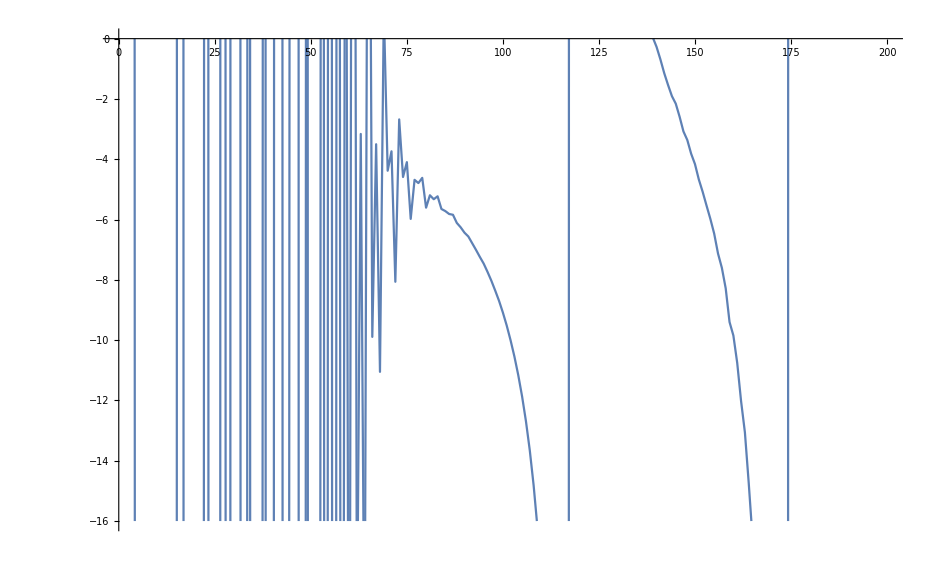

```mathematica
LmodePosition =3;
GridePosition  = 1;
l1mode = ConstantArray[0,tend];
Do[l1mode[[i]]=tails[i,LmodePosition,GridePosition],
{i,2,tend}]
ListPlot[l1mode,Joined->True,PlotRange->{0,-16}]
```

```mathematica
l1mode = ConstantArray[0,tend];
```

```mathematica
listRepeated=Table[ ConstantArray[0,tend],numberLmodes];
```

```mathematica
Do[
Do[listRepeated[[j]][[i]]=tails[i,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}

]
```

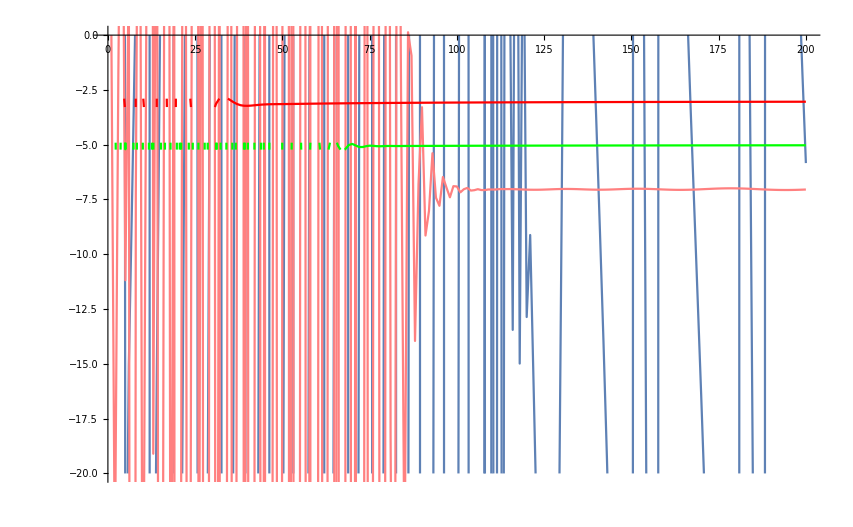

```mathematica
ListPlot[listRepeated[[1]],Joined->True, PlotStyle->Red];
ListPlot[listRepeated[[2]],Joined->True, PlotStyle->Green];
ListPlot[listRepeated[[3]],Joined->True, PlotStyle->Pink];
ListPlot[listRepeated[[4]],Joined->True,PlotRange->{0,-20}];
Show[%,%%,%%%,%%%%]
```